```mathematica
(*Basic definition *)
```

```mathematica
sig0 = {{1, 0},{0,1}};
sig1 = {{0,1},{1,0}} ;
sig2 = {{0,-I},{I,0}};
sig3 = {{1,0},{0,-1}};
l2[o_,r_] := ⅇ^(o √(1-1/r));
hbin[p_]:=Piecewise[{{-p Log[2,p]-(1-p) Log[2,1-p],0<p<1},{p,p==0},{p-1,p==1}}] ;
hbin[(2-√3)/4];
N[%];
c1=1;c2=-1;c3=1;

(*Expression for Subscript[ρ, AI]*)
Clear[part1,part2,part3,part4,part5,rouAI,eigRouAI];
part1[c3_] := c3* KroneckerProduct[ sig3, sig3] ;
part2 := KroneckerProduct[sig0, {{1,0},{0,0}}];
part3[o_,r_] := (3+l2[o,r]+ 2/l2[o,r])/(1 + l2[o,r]) * KroneckerProduct[sig0, ({{0, 0}, {0, 1}})];
part4[c1_,o_,r_] :=  c1 √(1+1/l2[o,r]) * KroneckerProduct[sig1, sig1];
part5[c2_,o_,r_] := c2  √(1+1/l2[o,r])* KroneckerProduct[sig2, sig2]  ;
rouAI[c1_,c2_,c3_,o_,r_] = 1/4 1/(1+ⅇ^(-o √(1-1/r)))(part1[c3]+part2+part3[o,r]+part4[c1,o,r]+part5[c2,o,r]);

(*?rouAI*)
rouAI[1,-1,1,10,1.00];
eigRouAI[c1_,c2_,c3_,o_,r_]  = Simplify[Eigenvalues[rouAI[1,-1,1,50,1.00]]]
```

{0.75,0.25,2.77556×10^-17,0.}

```mathematica
(*---------------------- Subscript[S, Subscript[ρ, I]] ---------------------*)
Clear[rouI,eigRouI,sRouI];
rouI[c1_,c2_,c3_,o_,r_]  = rouAI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouAI[c1,c2,c3,o,r][[3;;4,3;;4]];
rouI[c1,c2,c3,50,1.00]
eigRouI[c1_,c2_,c3_,o_,r_]  = Simplify[rouI[c1,c2,c3,o,r]][[1,1]]
sRouI[c1_,c2_,c3_,o_,r_]  := hbin[eigRouI[c1,c2,c3,o,r]];
sRouI[c1_,c2_,c3_,o_,r_]  = Simplify[sRouI[c1,c2,c3,o,r]];
sRouI[c1,c2,c3,50,1.00]
```

{{0.25,0},{0,0.75}}

1/(2 (1+ⅇ^(-o √((-1+r)/r))))

0.811278

```mathematica
(*---------------------- Subscript[S, Subscript[σ, x]] ---------------------*)
(* S(Subscript[ρ^Subscript[σ, x], Subscript[I, 0]]) in Subscript[S, σ^x] *)
Clear[rouX0,rouX0AI,rouIX0,pX0,eigRouIX0,sRouIX0];
rouX0:= KroneckerProduct[({{1/2, 1/2}, {1/2, 1/2}}),sig0];
rouX0AI[c1_,c2_,c3_,o_,r_] := rouX0.rouAI[c1,c2,c3,o,r];
rouIX0[c1_,c2_,c3_,o_,r_] := rouX0AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouX0AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pX0[c1_,c2_,c3_,o_,r_] = Simplify[Tr[rouIX0[c1,c2,c3,o,r]]]
rouIX0[c1_,c2_,c3_,o_,r_] = rouIX0[c1,c2,c3,o,r]/pX0[c1,c2,c3,o,r];
eigRouIX0[c1_,c2_,c3_,o_,r_] :=Eigenvalues[rouIX0[c1,c2,c3,o,r]];
eigRouIX0[c1_,c2_,c3_,o_,r_] = Simplify[eigRouIX0[c1,c2,c3,o,r]] ;
sRouIX0[c1_,c2_,c3_,o_,r_] := hbin[eigRouIX0[c1,c2,c3,o,r][[1]]];
sRouIX0[c1_,c2_,c3_,o_,r_] = Simplify[sRouIX0][c1,c2,c3,o,r];
sRouIX0[1,-1,1,50,1.00]
```

1/2

0.354579

```mathematica
(* S(Subscript[ρ^Subscript[σ, x], Subscript[I, 1]]) in Subscript[S, σ^x] *)
Clear[rouX1,rouX1AI,rouIX1,pX1,eigRouIX1,sRouIX1];
rouX1 := KroneckerProduct[({{1/2, -1/2}, {-1/2, 1/2}}),sig0];
rouX1AI[c1_,c2_,c3_,o_,r_] := rouX1.rouAI[c1,c2,c3,o,r];
rouIX1[c1_,c2_,c3_,o_,r_] := rouX1AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouX1AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pX1[c1_,c2_,c3_,o_,r_] = Tr[rouIX1[c1,c2,c3,o,r]];
Simplify[pX1[c1,c2,c3,o,r]]
rouIX1[c1_,c2_,c3_,o_,r_] = rouIX1[c1,c2,c3,o,r]/pX1[c1,c2,c3,o,r];
eigRouIX1[c1_,c2_,c3_,o_,r_] := Eigenvalues[rouIX1[c1,c2,c3,o,r]];
eigRouIX1[c1_,c2_,c3_,o_,r_] = Simplify[eigRouIX1[c1,c2,c3,o,r]];
sRouIX1[c1_,c2_,c3_,o_,r_] := hbin[eigRouIX1[c1,c2,c3,o,r][[1]]];
sRouIX1[c1_,c2_,c3_,o_,r_] =  Simplify[sRouIX1[c1,c2,c3,o,r]];
sRouIX1[1,-1,1,50,1.00]
```

1/2

0.354579

```mathematica
(* Subscript[S, Subscript[σ, x]] *)
Clear[sX]
(*pX0[1,-1,1,50,1.00]
sRouIX0[1,-1,1,50,1.00]
pX1[1,-1,1,50,1.00]
sRouIX1[1,-1,1,50,1.00]*)
sX[c1_,c2_,c3_,o_,r_] = pX0[c1,c2,c3,o,r] *sRouIX0[c1,c2,c3,o,r] + pX1[c1,c2,c3,o,r] * sRouIX1[c1,c2,c3,o,r];
sX[c1,c2,c3,o,r] = Simplify[sX[c1,c2,c3,o,r]];
sX[c1,c2,c3,50,1.00]
```

0.354579

```mathematica
(*----------------------------Subscript[S, σ^y]--------------------------*)
(* S(Subscript[ρ^Subscript[σ, y], Subscript[I, 0]]) in Subscript[S, σ^y] *)
Clear[rouY0,rouY0AI,rouIY0,pY0,eigRouIY0,sRouIY0];
rouY0:=KroneckerProduct[({{1/2,-I/2},{I/2,1/2}}),sig0];
rouY0AI[c1_,c2_,c3_,o_,r_]:=rouY0.rouAI[c1,c2,c3,o,r];
rouIY0[c1_,c2_,c3_,o_,r_]:=rouY0AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouY0AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pY0[c1_,c2_,c3_,o_,r_]=Tr[rouIY0[c1,c2,c3,o,r]];
pY0[1,-1,1,50,1.00]
rouIY0[c1_,c2_,c3_,o_,r_]=rouIY0[c1,c2,c3,o,r]/pY0[c1,c2,c3,o,r];
eigRouIY0[c1_,c2_,c3_,o_,r_]:=Eigenvalues[rouIY0[c1,c2,c3,o,r]];
eigRouIY0[c1_,c2_,c3_,o_,r_]=Simplify[eigRouIY0[c1,c2,c3,o,r]];
sRouIY0[c1_,c2_,c3_,o_,r_]:=hbin[eigRouIY0[c1,c2,c3,o,r][[1]]];
sRouIY0[c1_,c2_,c3_,o_,r_]=Simplify[sRouIY0][c1,c2,c3,o,r];
sRouIY0[1,-1,1,50,1.00]
```

0.5

0.354579

```mathematica
(* S(Subscript[ρ^Subscript[σ, y], Subscript[I, 1]]) in Subscript[S, σ^y] *)
Clear[rouY1,rouY1AI,rouIY1,pY1,eigRouIY1,sRouIY1];
rouY1 := KroneckerProduct[({{1/2, I/2}, {-I/2, 1/2}}),sig0];
rouY1AI[c1_,c2_,c3_,o_,r_] := rouY1.rouAI[c1,c2,c3,o,r];
rouIY1[c1_,c2_,c3_,o_,r_] := rouY1AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouY1AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pY1[c1_,c2_,c3_,o_,r_] = Tr[rouIY1[c1,c2,c3,o,r]];
pY1[1,-1,1,50,1.00]
rouIY1[c1_,c2_,c3_,o_,r_] = rouIY1[c1,c2,c3,o,r]/pY1[c1,c2,c3,o,r];
eigRouIY1[c1_,c2_,c3_,o_,r_] := Eigenvalues[rouIY1[c1,c2,c3,o,r]];
eigRouIY1[c1_,c2_,c3_,o_,r_] = Simplify[eigRouIY1[c1,c2,c3,o,r]];
sRouIY1[c1_,c2_,c3_,o_,r_] := hbin[eigRouIY1[c1,c2,c3,o,r][[1]]];
sRouIY1[c1_,c2_,c3_,o_,r_] =  Simplify[sRouIY1[c1,c2,c3,o,r]];
sRouIY1[1,-1,1,50,1.00]
```

0.5

0.354579

```mathematica
(* Subscript[S, Subscript[σ, y]] *)
Clear[sY]
sY[c1_,c2_,c3_,o_,r_] = pY0[c1,c2,c3,o,r] *sRouIY0[c1,c2,c3,o,r] + pY1[c1,c2,c3,o,r] * sRouIY1[c1,c2,c3,o,r];
sY[c1,c2,c3,o,r] = Simplify[sY[c1,c2,c3,o,r]];
sY[c1,c2,c3,50,1.00]
```

0.354579

```mathematica
(*----------------------------Subscript[S, σ^z]--------------------------*)
(* S(Subscript[ρ^Subscript[σ, z], Subscript[I, 0]]) in Subscript[S, σ^z] *)
Clear[rouZ0,rouZ0AI,rouIZ0,pZ0,eigRouIZ0,sRouIZ0];
rouZ0=KroneckerProduct[({{0,0},{0,1}}),sig0];
rouZ0AI[c1_,c2_,c3_,o_,r_]:=rouZ0.rouAI[c1,c2,c3,o,r];
rouIZ0[c1_,c2_,c3_,o_,r_]:=rouZ0AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouZ0AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pZ0[c1_,c2_,c3_,o_,r_]=Tr[rouIZ0[c1,c2,c3,o,r]];
Simplify[pZ0[c1,c2,c3,o,r]]
rouIZ0[c1_,c2_,c3_,o_,r_]=rouIZ0[c1,c2,c3,o,r]/pZ0[c1,c2,c3,o,r];
eigRouIZ0[c1_,c2_,c3_,o_,r_]:=Eigenvalues[rouIZ0[c1,c2,c3,o,r]];
eigRouIZ0[c1_,c2_,c3_,o_,r_]=Simplify[eigRouIZ0[c1,c2,c3,o,r]]
sRouIZ0[c1_,c2_,c3_,o_,r_]=0;
```

1/2

{1,0}

```mathematica
(* S(Subscript[ρ^Subscript[σ, z], Subscript[I, 1]]) in Subscript[S, σ^z] *)
Clear[rouZ1,rouZ1AI,rouIZ1,pZ1,eigRouIZ1,sRouIZ1];
rouZ1 := KroneckerProduct[({{1, 0}, {0, 0}}),sig0];
rouZ1AI[c1_,c2_,c3_,o_,r_] := rouZ1.rouAI[c1,c2,c3,o,r];
rouIZ1[c1_,c2_,c3_,o_,r_] := rouZ1AI[c1,c2,c3,o,r][[1;;2,1;;2]]+rouZ1AI[c1,c2,c3,o,r][[3;;4,3;;4]];
pZ1[c1_,c2_,c3_,o_,r_] = Tr[rouIZ1[c1,c2,c3,o,r]];
Simplify[pZ1[c1,c2,c3,o,r]]
rouIZ1[c1_,c2_,c3_,o_,r_] = rouIZ1[c1,c2,c3,o,r]/pZ1[c1,c2,c3,o,r];
eigRouIZ1[c1_,c2_,c3_,o_,r_] := Eigenvalues[rouIZ1[c1,c2,c3,o,r]];
eigRouIZ1[c1_,c2_,c3_,o_,r_] = Simplify[eigRouIZ1[c1,c2,c3,o,r]]
sRouIZ1[c1_,c2_,c3_,o_,r_] := hbin[eigRouIZ1[c1,c2,c3,o,r][[1]]];
sRouIZ1[c1_,c2_,c3_,o_,r_] =  Simplify[sRouIZ1[c1,c2,c3,o,r]];
sRouIZ1[1,-1,1,50,1.00]
```

1/2

{1/(1+ⅇ^(o √((-1+r)/r))),ⅇ^(o √((-1+r)/r))/(1+ⅇ^(o √((-1+r)/r)))}

1.

```mathematica
(* Subscript[S, Subscript[σ, z]] *)
Clear[sZ]
sZ[c1_,c2_,c3_,o_,r_] = pZ0[c1,c2,c3,o,r] *sRouIZ0[c1,c2,c3,o,r] + pZ1[c1,c2,c3,o,r] * sRouIZ1[c1,c2,c3,o,r];
sZ[c1,c2,c3,o,r] = Simplify[sZ[c1,c2,c3,o,r]];
sZ[c1,c2,c3,50,1.00]
```

0.5

1.0866

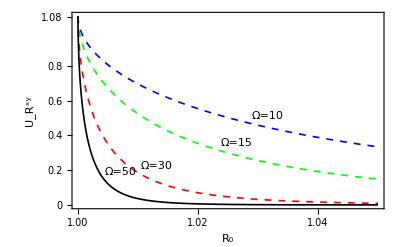

```mathematica
(*----------------------------Subscript[Q, 2]^xy--------------------------*)
Clear[q2XY];
q2XY[c1_,c2_,c3_,o_,r_] = -2 *sRouI[c1,c2,c3,o,r] + sX[c1,c2,c3,o,r] + sY[c1,c2,c3,o,r];
q2XY[c1,c2,c3,50,1.00]+2
g1 = Plot[{q2XY[c1,c2,c3,10,r]+2,q2XY[c1,c2,c3,15,r]+2,q2XY[c1,c2,c3,30,r]+2,q2XY[c1,c2,c3,50,r]+2}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_R^xy"},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1.08},None},{All,None}},RotateLabel->False,PlotStyle->{{Dashed,Blue,Thickness[0.003]},{Dashed,Green,Thickness[0.003]},{Dashed,Red,Thickness[0.003]},{Black,Thickness[0.003]}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

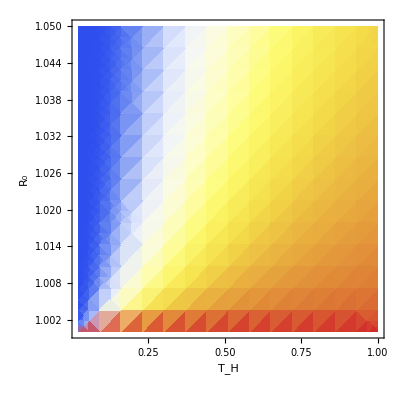

```mathematica
g2 = DensityPlot[q2XY[c1,c2,c3,3/t,r]+2,{t,0.02,1},{r,1,1.05},Frame->True,FrameLabel -> {{"R_0",""},{"T_H","U_R^xy"}},RotateLabel->False,ColorFunction->"TemperatureMap"]
```

1.23202

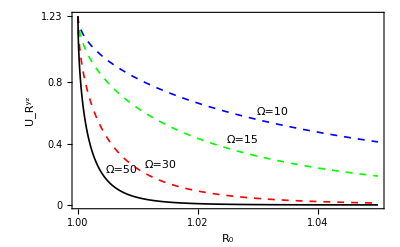

```mathematica
(*----------------------------Subscript[Q, 2]^yz--------------------------*)
Clear[q2YZ];
q2YZ[c1_,c2_,c3_,o_,r_] = -2 *sRouI[c1,c2,c3,o,r] + sY[c1,c2,c3,o,r] + sZ[c1,c2,c3,o,r];
q2YZ[c1,c2,c3,50,1.00]+2
Plot[{q2YZ[c1,c2,c3,10,r]+2,q2YZ[c1,c2,c3,15,r]+2,q2YZ[c1,c2,c3,30,r]+2,q2YZ[c1,c2,c3,50,r]+2}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_R^yz"},RotateLabel->False,FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.23},None},{All,None}},PlotStyle->{{Dashed,Blue,Thickness[0.003]},{Dashed,Green,Thickness[0.003]},{Dashed,Red,Thickness[0.003]},{Black,Thickness[0.003]}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

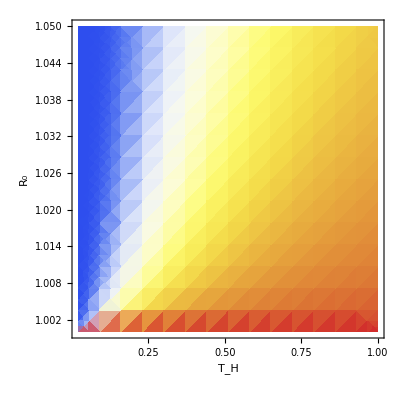

```mathematica
DensityPlot[q2YZ[c1,c2,c3,3/t,r]+2,{t,0.02,1},{r,1,1.05},Frame->True,FrameLabel -> {{"R_0",""},{"T_H","U_R^yz"}},RotateLabel->False,ColorFunction->"TemperatureMap"]
```

1.23202

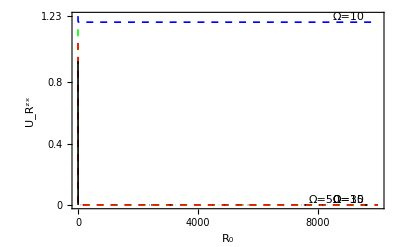

```mathematica
(*----------------------------Subscript[Q, 2]^zx--------------------------*)
Clear[q2ZX];
q2ZX[c1_,c2_,c3_,o_,r_] = -2 *sRouI[c1,c2,c3,o,r] + sZ[c1,c2,c3,o,r] + sX[c1,c2,c3,o,r];
q2ZX[c1,c2,c3,50,1.00]+2
Plot[{q2ZX[c1,c2,c3,0.1,r]+2,q2ZX[c1,c2,c3,15,r]+2,q2ZX[c1,c2,c3,30,r]+2,q2ZX[c1,c2,c3,50,r]+2},{r,1,10000.05},Frame->True,FrameLabel->{"R_0","U_R^zx"},RotateLabel->False,FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.23},None},{All,None}},PlotStyle->{{Dashed,Blue,Thickness[0.003]},{Dashed,Green,Thickness[0.003]},{Dashed,Red,Thickness[0.003]},{Black,Thickness[0.003]}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
DensityPlot[q2ZX[c1,c2,c3,3/t,r]+2,{t,0.02,1},{r,1,1.05},Frame->True,FrameLabel -> {{"R_0",""},{"T_H","U_R^zx"}},RotateLabel->False,ColorFunction->"TemperatureMap"]
```

-Graphics-

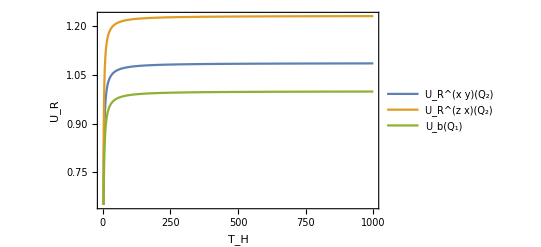

```mathematica
q1[o_,r_] = 1+ hbin[1/(2+2 l2[o,r])] -hbin[l2[o,r]/(2+2 l2[o,r])];
r00 = 1000.55;
Plot[{q2XY[c1,c2,c3,3/t,r00]+2,q2ZX[c1,c2,c3,3/t,r00]+2, q1[3/t,r00]},{t,0.1,1000},Frame->True,FrameLabel->{{"U_R",""},{"T_H","R_0=1.02"}},RotateLabel->False,PlotLegends->Placed[{"U_R^(x y)(Q_2)","U_R^(z x)(Q_2)","U_b(Q_1)"},{0.8,0.5}]]
```

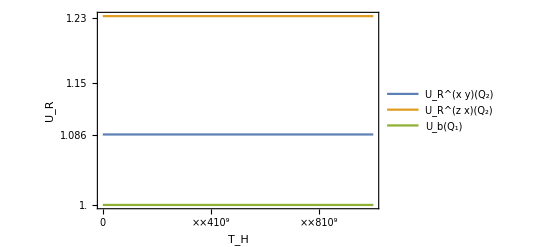

```mathematica
Plot[{q2XY[c1,c2,c3,3/t,1.0]+2,q2ZX[c1,c2,c3,3/t,1.0]+2,1},{t,0.00,10000000000},Frame->True,FrameLabel->{{"U_R",""},{"T_H","R_0=1"}},RotateLabel->False,PlotLegends->Placed[{"U_R^(x y)(Q_2)","U_R^(z x)(Q_2)","U_b(Q_1)"},{0.8,0.65}],FrameTicks->{{{1.00,1.05,1.086,1.10,1.15,1.20,1.23},None},{All,None}}]
```

```mathematica
rou12 = ({{1/4, 0, 0, 1/4}, {0, 0, 0, 0}, {0, 0, 1/2, 0}, {1/4, 0, 0, 1/4}});
Eigenvalues[rou12]
```

{1/2,1/2,0,0}

```mathematica
hbin[1/4]
```

(3 Log[4/3])/(4 Log[2])+Log[4]/(4 Log[2])

```mathematica
N[%]
```

0.811278

```mathematica
Clear[l1,l2];
ini = ({{a l1^2, 0, b*l1, a l1 l2}, {0, 0, 0, 0}, {r l1, 0, w, r l2}, {a l1 l2, 0, b l2, a l2^2}});
```

```mathematica
Clear[l1,l2];Clear[a,b,r,w]; a = a1^2; b = a1 b1; r = b1 a1; w = b1^2;(*l1 = 1/(√2); l2 = 1/(√2);*)l2 = √(1-l1^2); b1 = √(1-a1^2);
Eigenvalues[ini]
```

{1,0,0,0}

```mathematica
a = a1^2; b = a1 b1; r = b1 a1; w = b1^2;Clear[l1,l2]; l2 = √(1-l1^2); b1 = √(1-a1^2); l1 = 1/(√2); a1 = 1;Clear[a1];a = a1^2; b = a1 b1; r = b1 a1; w = b1^2;Clear[a,b,r,w];
Clear[l1,l2];a=1/2;b=0;r=0;w=1/2;l1=√(1-l2^2);
Simplify[({{a l1^2+w, r l2}, {b l2, a l2^2}})] //MatrixForm
Simplify[({{a l1^2, b l1}, {r l1, w+a l2^2}})]//MatrixForm

Simplify[Eigenvalues[({{a l1^2+w, r l2}, {b l2, a l2^2}})]]
Simplify[Eigenvalues[({{a l1^2, b l1}, {r l1, w+a l2^2}})]]
```

(1-l2^2/2 | 0
0 | l2^2/2)

(1/2 (1-l2^2) | 0
0 | 1/2 (1+l2^2))

{l2^2/2,1-l2^2/2}

{1/2 (1-l2^2),1/2 (1+l2^2)}

```mathematica
Solve[x^2+a x+1==0,x];
```

{{x→1/4 (-1-ⅈ √15)},{x→1/4 (-1+ⅈ √15)}}

```mathematica
Clear[p,x];
hbin[p_] := Piecewise[{{-p*Log[2,p]-(1-p)*Log[2,(1-p)], 0<p<1}, {0, p==0}, {0, p==1}}]
(*NSolve[hbin[p]==1,p]*)
?hbin
hbin[1/4]
```

Global`hbin

hbin[p_]:=Piecewise[{{-p Log[2,p]-(1-p) Log[2,1-p],0<p<1},{0,p==0},{0,p==1}}]

1/2+(3 Log[4/3])/(4 Log[2])

```mathematica
Clear[p,hbin];
hbin[p_]:=Piecewise[{{-p Log[2,p]-(1-p) Log[2,1-p],0<p<1},{p,p==0},{p-1,p==1}}] 
NSolve[hbin[p/2]+hbin[1/2-p/2]==1+(3 Log[4/3])/(E 2Log[2]),p]
hbin[1/4]
```

{{p→0.0760677},{p→0.923932}}

1/2+(3 Log[4/3])/(4 Log[2])

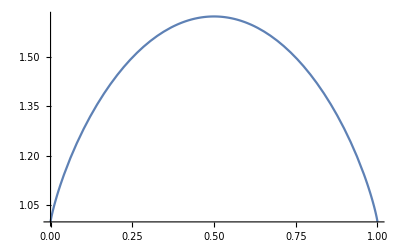

```mathematica
Clear[hh];
hh[p_]:=hbin[p/2]+hbin[1/2-p/2];
Plot[hh[p],{p,0,1}]
```

```mathematica
Clear[l1,l2];l1=√(1-l2^2);
Simplify[Eigenvalues[({{l1^2/2, 0, 0, (l1 l2)/2}, {0, 0, 0, 0}, {0, 0, 1/2, 0}, {(l1 l2)/2, 0, 0, l2^2/2}})]]
```

{1/2,1/2,0,0}

```mathematica
N[E]
```

2.71828

```mathematica
FindRoot[-((1-p) Log[1-p])/Log[2]-(p Log[p])/Log[2]==1,{p,1/3}]
```

{p→0.5}

```mathematica
hbin[1]
```

Infinity::indet: Indeterminate expression (0 (-∞))/Log[2] encountered.

Indeterminate

```mathematica
Piecewise[{{x^2,x<0},{x,x>0}}]/.x->1
```

1

```mathematica
(Log[0.076])^2/4
```

1.66026

```mathematica
%/8^2
```

0.0259416

```mathematica
(Log[1/0.924-1])^2
```

6.2399

```mathematica
%/8
```

0.779987